(1 | 0
0 | 1)

{0,1}

{1,0}

1

1

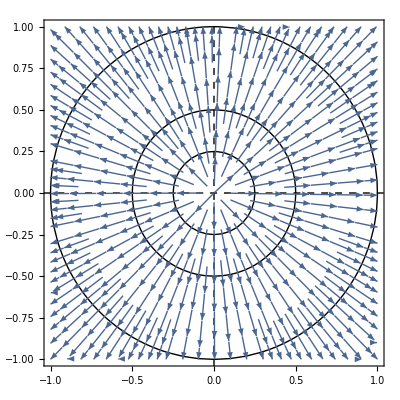

```mathematica
r=1;
a={{1,0},{0,1}};
MatrixForm@a
h1=Eigensystem[a]⟦2,1⟧
h2=Eigensystem[a]⟦2,2⟧
λ1=Eigensystem[a]⟦1,1⟧
λ1=Eigensystem[a]⟦1,2⟧

StreamPlot[{(a.{x,y})⟦1⟧,(a.{x,y})⟦2⟧},{x,-r,r},{y,-r,r}, MeshFunctions->{Function[{x,y,vx,vy,n},h1.{-y,x}],Function[{x,y,vx,vy,n},h2.{-y,x}],Function[{x,y,vx,vy,n},n]}, Mesh->{1,1,{0.25,0.5,1,1.5}},MeshStyle->{{Thick, Dashed,},{Thick, Dashed,},{}},StreamPoints->Fine]
```